```mathematica
u090494e　荒井直幸　2014年10月14日
```

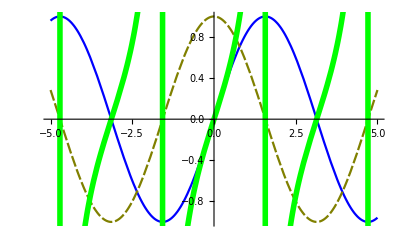

```mathematica
g1=Plot[Sin[x],{x,-5,5},PlotStyle->RGBColor[0,0,1]];
g2=Plot[Cos[x],{x,-5,5},PlotStyle->{RGBColor[0.5,0.5,0],Dashing[{0.02,0.005}]}];
g3=Plot[Tan[x],{x,-5,5},PlotStyle->{RGBColor[0,1,0],Thickness[0.01]}];
Show[g1,g2,g3]
```

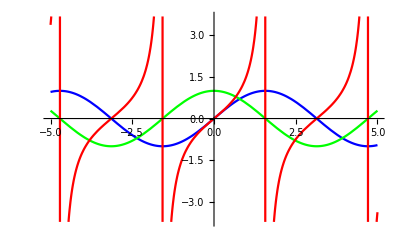

```mathematica
Plot[{Sin[x],Cos[x],Tan[x]},{x,-5,5},PlotStyle->{RGBColor[0,0,1],RGBColor[0,1,0],RGBColor[1,0,0]}]
```

{{0,1},{0.4,0.8},{0.8,0.4},{1,0},{0.8,-0.4}}

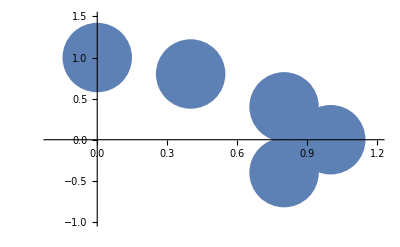

```mathematica
data={{0,1},{0.4,0.8},{0.8,0.4},{1,0},{0.8,-0.4}}
ListPlot[data,PlotStyle->PointSize[0.2],PlotRange->{{-0.2,1.2},{-1,1.5}}]
```

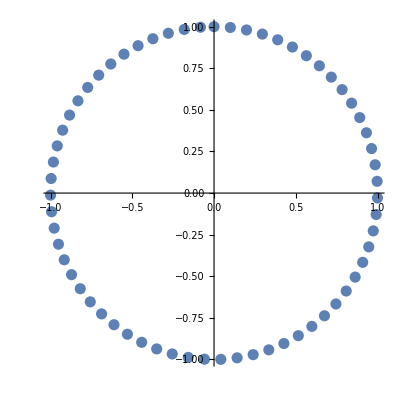

```mathematica
data1=Table[{Sin[a],Cos[a]},{a,0,2 Pi,0.1}];
ListPlot[data1,PlotStyle->PointSize[0.02],AspectRatio->1]
```

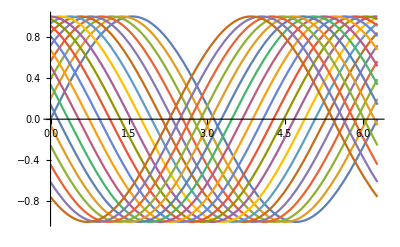

```mathematica
data2=Table[Sin[a+c],{c,0,4,0.2}];
Plot[data2,{a,0,2 Pi}]
```

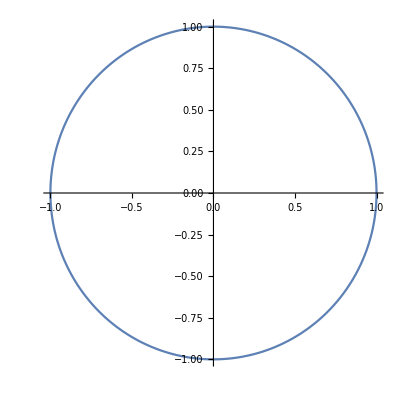

```mathematica
ParametricPlot[{Sin[x],Cos[x]},{x,0,2 Pi}]
```

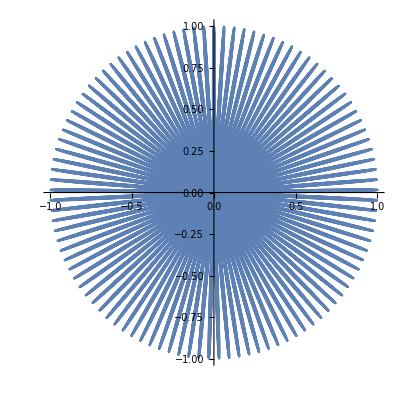

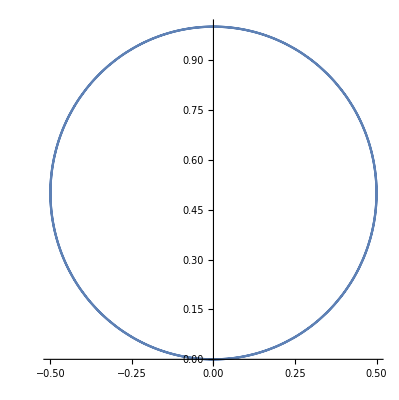

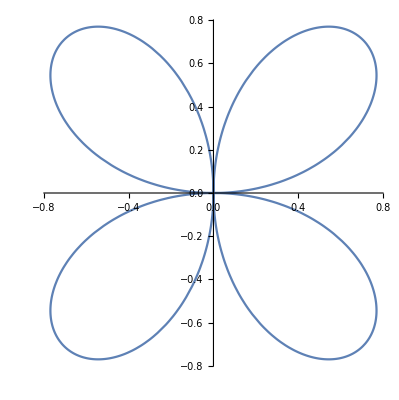

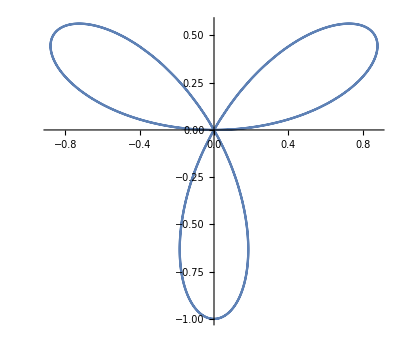

```mathematica
ParametricPlot[{Sin[i x] Cos[x],Sin[i x] Sin[x]},{x,0,2 Pi}]
i=1;
While[i≤3,Print[ParametricPlot[{Sin[i x] Cos[x],Sin[i x] Sin[x]},{x,0,2 Pi}]];i=i+1]
```

6.62607×10^-34

2.99792×10^8

1.38065×10^-23

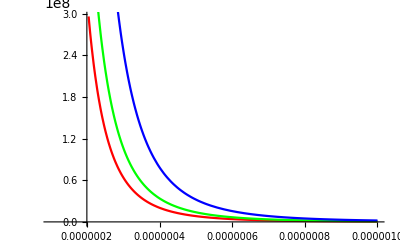

```mathematica
h=6.62607*10^(-34)
c=2.99792458*10^8
k=1.38065*10^(-23)
classic[t_]:=(8π k t)/λ^4
graph1=Plot[classic[1500],{λ,100*10^(-9),1000*10^(-9)},PlotStyle->RGBColor[1,0,0]];
graph2=Plot[classic[2500],{λ,100*10^(-9),1000*10^(-9)},PlotStyle->RGBColor[0,1,0]];
graph3=Plot[classic[5800],{λ,100*10^(-9),1000*10^(-9)},PlotStyle->RGBColor[0,0,1]];
Show[graph1,graph2,graph3]
```

```mathematica
課題１
```

```mathematica
それぞれの値は
```

```mathematica
h=6.62607*10^(-34)
c=2.99792458*10^8
k=1.38065*10^(-23)
```

6.62607×10^-34

2.99792×10^8

1.38065×10^-23

```mathematica
プランクの式は
```

```mathematica
puranku[t_]:=(8π h c)/(λ^5*(Exp[(h c)/(λ k t)]-1))
```

```mathematica
それぞれの場合についてプロットすると
```

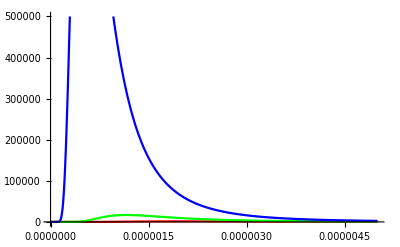

```mathematica
graph4=Plot[puranku[1500],{λ,0,5000*10^(-9)},PlotRange->{0,500000},PlotStyle->RGBColor[1,0,0]];
graph5=Plot[puranku[2500],{λ,0,5000*10^(-9)},PlotRange->{0,500000},PlotStyle->RGBColor[0,1,0]];
graph6=Plot[puranku[5800],{λ,0,5000*10^(-9)},PlotRange->{0,500000},PlotStyle->RGBColor[0,0,1]];
Show[graph4,graph5,graph6]
```